```mathematica
SetDirectory["G:\\johnny\\matlab\\jlhbpe\\2016_10_projects"]
```

G:\johnny\matlab\jlhbpe\2016_10_projects

```mathematica
bockrisSwinkel[betaInv_,f_,n_,theta_]:=betaInv*Exp[-f*theta]*theta/(1-theta)^n*(theta+n*(1-theta))^(n-1)/n^n
```

```mathematica
massBockrisSwinkel[betaInv_,f_,n_,m0_,mErr_,m_]:=bockrisSwinkel[betaInv,f,n,(m-mErr)/m0]
```

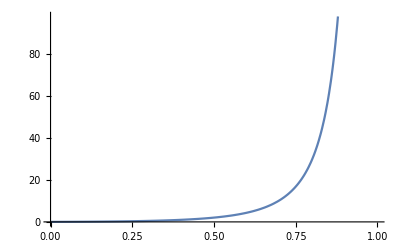

```mathematica
Plot[bockrisSwinkel[1,-2,2,theta],{theta,0,1}]
```

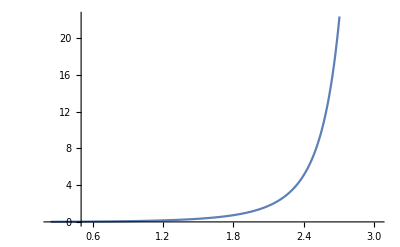

```mathematica
Plot[massBockrisSwinkel[1,-2,10,3.5*^-7,0,m],{m,2.39*^-8,3.03*^-7}]
```

```mathematica
Manipulate[Plot[massBockrisSwinkel[betaInv,f,n,m0,mErr,m],{m,2.39*^-8,3.03*^-7}],{{betaInv,1},0,10},{{n,10},0,30},{{f,-2},-10,10},{{m0,3.5*^-7},3*^-7,3*^-6},{{mErr,0},-3*^-7,3*^-7}]
```

```mathematica
mNum[betaInv_,f_,n_,m0_,mErr_,c_]:=m/.NSolve[massBockrisSwinkel[betaInv,f,n,m0,mErr,m]==c&&m-mErr<m0,m,Reals][[1]]
```

```mathematica
mRoot[betaInv_,f_,n_,m0_,mErr_,c_]:=m/.FindRoot[massBockrisSwinkel[betaInv,f,n,m0,mErr,m]==c,{m,(m0+mErr)/2}]
```

```mathematica
Quiet[mNum[1,-2.8,10,3.5*^-7,0,4]]
```

2.1988×10^-7

```mathematica
mRoot[1,-2.8,10,3.5*^-7,0,4]
```

2.1988×10^-7

```mathematica
Manipulate[Plot[Quiet[mNum[betaInv,f,n,m0,mErr,c]],{c,3.46*^-4,137}],{{betaInv,1},0,10},{{n,10},0,30},{{f,-2},-10,10},{{m0,3.5*^-7},3*^-7,3*^-6},{{mErr,0},-3*^-7,3*^-7}]
```

```mathematica
adMass1mA=Import["zhang2015control_adsorption_mass_fig4_0_1mA.txt","Table"][[3;;]];
```

```mathematica
adMass2mA=Import["zhang2015control_adsorption_mass_fig4_0_2mA.txt","Table"][[3;;]];
```

```mathematica
adMass4mA=Import["zhang2015control_adsorption_mass_fig4_0_4mA.txt","Table"][[3;;]];
```

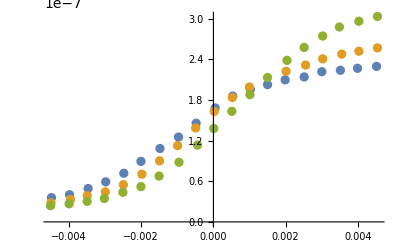

```mathematica
trueMassPlot=ListPlot[{adMass1mA,adMass2mA,adMass4mA}]
```

```mathematica
dat1mA=Import["zhang2015control_surface_data_0_1mA.txt","Data"][[2;;]];
```

```mathematica
dat2mA=Import["zhang2015control_surface_data_0_2mA.txt","Data"][[2;;]];
```

```mathematica
dat4mA=Import["zhang2015control_surface_data_0_4mA.txt","Data"][[2;;]];
```

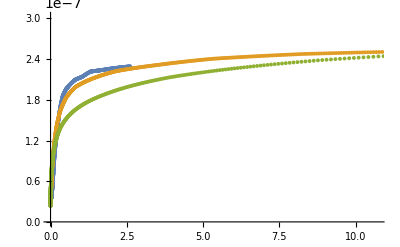

```mathematica
refPlot=ListPlot[{Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

```mathematica
refIsotherm1mA=Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}];
```

```mathematica
refIsotherm2mA=Table[{dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}];
```

```mathematica
refIsotherm4mA=Table[{dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseIsotherm1mA=Table[{dat1mA[[n]][[3]],dat1mA[[n]][[2]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseIsotherm2mA=Table[{dat2mA[[n]][[3]],dat2mA[[n]][[2]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseIsotherm4mA=Table[{dat4mA[[n]][[3]],dat4mA[[n]][[2]]},{n,1,Length[dat4mA]}];
```

```mathematica
refReverseLogIsotherm1mA=Table[{dat1mA[[n]][[3]],Log[dat1mA[[n]][[2]]]},{n,1,Length[dat1mA]}];
```

```mathematica
refReverseLogIsotherm2mA=Table[{dat2mA[[n]][[3]],Log[dat2mA[[n]][[2]]]},{n,1,Length[dat2mA]}];
```

```mathematica
refReverseLogIsotherm4mA=Table[{dat4mA[[n]][[3]],Log[dat4mA[[n]][[2]]]},{n,1,Length[dat4mA]}];
```

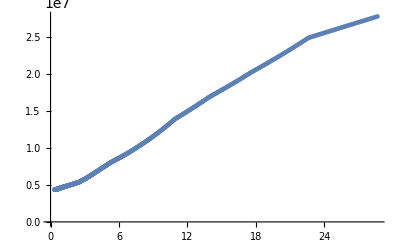

```mathematica
ListPlot[{1/Table[{dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}]}]
```

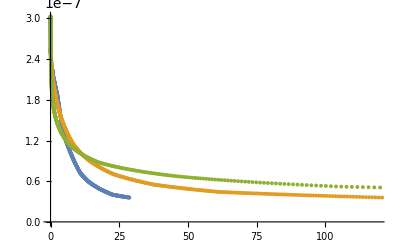

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

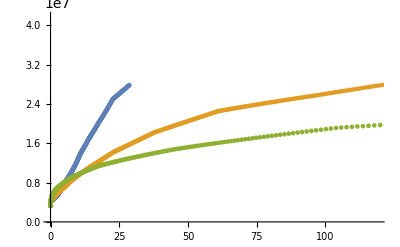

```mathematica
ListPlot[{Table[{1/dat1mA[[n]][[2]],1/dat1mA[[n]][[3]]},{n,1,Length[dat1mA]}],
Table[{1/dat2mA[[n]][[2]],1/dat2mA[[n]][[3]]},{n,1,Length[dat2mA]}],
Table[{1/dat4mA[[n]][[2]],1/dat4mA[[n]][[3]]},{n,1,Length[dat4mA]}]}]
```

```mathematica
Manipulate[Show[refPlot,
Plot[Quiet[mNum[betaInv,f,n,m0,mErr,c]],
{c,3.465*^-4,20},PlotStyle->{Thick,Automatic,Red,Dashed},Mesh->All,MaxRecursion->6,PlotPoints->50],PlotRange->{{0,20},All}],
{{betaInv,2},0,10},{{n,10},0,30},{{f,-2},-10,10},{{m0,3.5*^-7},3*^-7,3*^-6},{{mErr,0},-3*^-7,3*^-7}]
```

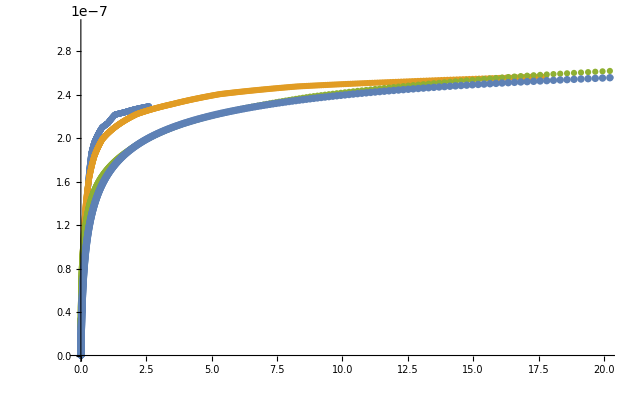

```mathematica
Show[refPlot,ListPlot[testIsotherm],PlotRange->{{0,20},All}]
```

## Reference Plots :

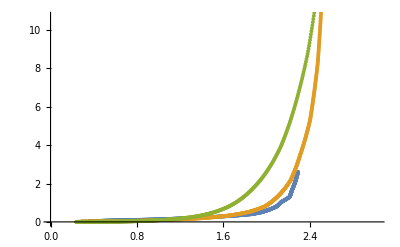

```mathematica
refReverseIsothermPlot=ListPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

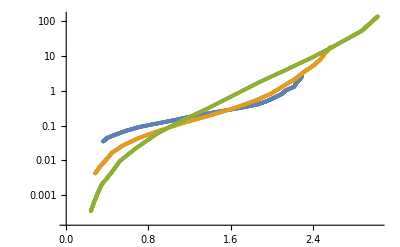

```mathematica
refReverseIsothermLogPlot=ListLogPlot[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]
```

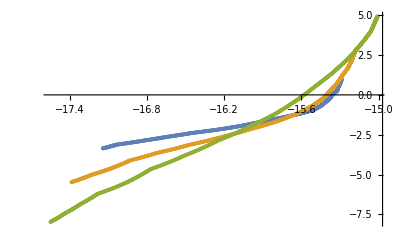

```mathematica
refReverseIsothermLogLogPlot=ListPlot[Log[{refReverseIsotherm1mA,refReverseIsotherm2mA,refReverseIsotherm4mA}]]
```

```mathematica
Manipulate[Show[refReverseIsothermPlot,Plot[massBockrisSwinkel[betaInv,f,n,m0,mErr,m],{m,2.39*^-8,3.03*^-7}]],{{betaInv,1},0,10},{{n,10},0,30},{{f,-2},-10,10},{{m0,3.5*^-7},3*^-7,5*3*^-7},{{mErr,0},-3*^-7,3*^-7}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[202]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[202]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[Show[refReverseIsothermPlot,Plot[massBockrisSwinkel[betaInv,f,n,m0,mErr,m],{m,2.39*^-8,3.03*^-7}]],{{betaInv,1},0,10},{{n,10},0,30},{{f,-2},-10,10},{{m0,3.5*^-7},3*^-7,5*3*^-7},{{mErr,0},-3*^-7,3*^-7}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[153]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[153]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[Show[refReverseIsothermLogPlot,Plot[Log[massBockrisSwinkel[betaInv,f,n,m0,mErr,m]],{m,2.39*^-8,3.03*^-7}]],{{betaInv,4.38},0,10},{{n,11.55},0,30},{{f,2.7},-10,10},{{m0,3*^-7},3*^-7,5*3*^-7},{{mErr,0},-3*^-7,3*^-7}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[76]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[Show[refReverseIsothermLogPlot,Plot[Log[massBockrisSwinkel[betaInv,f,n,m0,mErr,m]],{m,2.39*^-8,3.03*^-7}]],{{betaInv,3.74},0,10},{{n,22.5},0,30},{{f,0.25},-10,10},{{m0,3.03*^-7},3*^-7,5*3*^-7},{{mErr,2.04*^-8},-3*^-7,3*^-7}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[113]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[Show[refReverseIsothermLogPlot,Plot[Log[massBockrisSwinkel[betaInv,f,n,m0,mErr,m]],{m,2.39*^-8,3.03*^-7}]],{{betaInv,1.1},0,10},{{n,18.55},0,30},{{f,-6.82},-10,10},{{m0,4.008*^-7},3*^-7,5*3*^-7},{{mErr,2.28*^-8},-3*^-7,3*^-7}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[List[List[], List[], List[Directive[Opacity[1.`], RGBColor[0.368417`, 0.506779`, 0.709798`], AbsoluteThickness[1.6`]], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[75]]]]]], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
fit1mA=Block[{count=0},{FindFit[refReverseIsotherm1mA,
{massBockrisSwinkel[betaInv,f,n,m0,0,m],
{10>betaInv>0,-10<f<10,0.5<n<20,3.03*^-7<m0<3*^-6}},
{{betaInv,4.38},{f,2.7},{n,11.55},{m0,3.03*^-7}},m,MaxIterations->1000],count}];
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 1000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {2.56668×10^-6, 0.00017136, 5.88943×10^-7}, is returned.

```mathematica
fit1mA
```

{{betaInv→4.41265,f→-2.6282,n→11.5145,m0→1.58625×10^-6},0}

```mathematica
fit2mA=Block[{count=0},{FindFit[refReverseIsotherm2mA,
{massBockrisSwinkel[betaInv,f,n,m0,0,m],
{10>betaInv>0,-10<f<10,0.5<n<40,3.03*^-7<m0<3*^-6}},
{{betaInv,3.74},{f,-2},{n,22.5},{m0,3.03*^-7}},m,MaxIterations->1000],count}];
```

```mathematica
fit2mA
```

{{betaInv→0.384711,m0→3.25127×10^-7,mErr→0.},1}

```mathematica
fit4mA=Block[{count=0},{FindFit[refReverseIsotherm4mA,
{massBockrisSwinkel[betaInv,f,n,m0,mErr,m],
{10>betaInv>0,-10<f<10,0<n<30,0<m0-mErr<3*^-6,0<mErr<3*^-7}},
{{betaInv,1.1},{f,-6.82059},{n,18.55},{m0,4.008*^-7},{mErr,2.28*^-8}},m,MaxIterations->1000,Method->NMinimize],count}];
```

NMinimize::nnum: The function value TagBox[Experimental`NumericalFunction[« 1 »], False, Rule[Editable, False], Rule[SelectWithContents, True]] is not a number at {betaInv, f, m0, mErr, n} = {0.0038925, 9.03505, 5.62608×10^-6, 1.81461×10^-7, 0.00857545}.

```mathematica
fit2mA=Block[{count=0},{FindFit[refReverseIsotherm2mA,
{massBockrisSwinkel[betaInv,-2.82,20,m0,mErr,m],
{0<betaInv<10,3.03*^-7<m0,0<mErr<3*^-7}},
{{betaInv,3},{m0,3.03*^-7},{mErr,2.28*^-8}},m,EvaluationMonitor->count++,MaxIterations->1000,Method->NMinimize],count}];
```

```mathematica
fit2mA
```

{{betaInv→0.384711,m0→3.25127×10^-7,mErr→0.},1}

```mathematica
fit2mA
```

{{f→0.,mErr→0.},1}

```mathematica
fit4mA=Block[{count=0},{FindFit[refReverseIsotherm4mA,
{massBockrisSwinkel[1.1,f,18.55,4.008*^-7,2.28*^-8,m],
{-10<f<10}},
{{f,-6.85}},m,EvaluationMonitor->count++,MaxIterations->1000,Method->NMinimize],count}];
```

```mathematica
fit4mA=Block[{count=0},{FindFit[refReverseIsotherm4mA,
{massBockrisSwinkel[betaInv,-6.82059,18.55,4.008*^-7,2.28*^-8,m],
{0<betaInv<10}},
{{betaInv,1.1}},m,EvaluationMonitor->count++,MaxIterations->1000],count}];
```

```mathematica
fit4mA=Block[{count=0},{FindFit[refReverseIsotherm4mA,
{massBockrisSwinkel[1.09008,-6.82059,n,4*^-7,2.28*^-8,m],
{1<n<30}},
{{n,3}},m,EvaluationMonitor->count++,MaxIterations->1000],count}];
```

```mathematica
fit4mA=Block[{count=0},{FindFit[refReverseIsotherm4mA,
{massBockrisSwinkel[betaInv,-6.82059,19.0122,(4*^-7),mErr,m],
{0<betaInv<10,0<mErr<2.39*^-8}},
{{betaInv,0.5957},{mErr,1.11436*^-8}},m,EvaluationMonitor->count++,MaxIterations->1000,Method->NMinimize],count}];
```

```mathematica
fit4mA
```

{{betaInv→0.59572,mErr→1.11436×10^-8},1}

```mathematica
fit4mA
```

{{betaInv→1.09,mErr→2.151×10^-8},1}

```mathematica
fit4mA
```

{{n→19.0122},1}

```mathematica
fit4mA
```

{{f→-6.82059},1}

```mathematica
fit4mA
```

{{f→-5.1452,mErr→0.},1}

```mathematica
fit1mA[[1]]
```

{betaInv→4.41265,f→-2.6282,n→11.5145,m0→1.58625×10^-6}

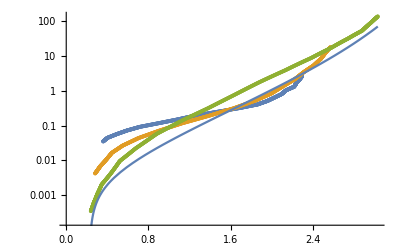

```mathematica
Show[refReverseIsothermLogPlot,Plot[Log[massBockrisSwinkel[0.59572,-6.82,19.0122,4*^-7,2.28*^-8,m]],{m,1.11436*^-8,3.03*^-7}]]
```

```mathematica
massBockrisSwinkel[betaInv,f,n,m0,mErr,m]/.fit1mA[[1]]
```

(0.00830532 ⅇ^(1.42157×10^6 (m-mErr)) (9.41906 (1-2.01741×10^6 (m-mErr))+2.01741×10^6 (m-mErr))^8.41906 (m-mErr))/(1-2.01741×10^6 (m-mErr))^9.41906

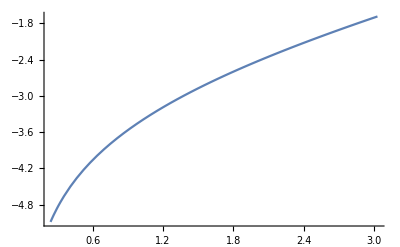

```mathematica
Plot[Log[Evaluate[massBockrisSwinkel[betaInv,f,n,m0,0,m]/.fit1mA[[1]]]],{m,2.39*^-8,3.03*^-7}]
```

```mathematica
fit4mALog=Block[{count=0},{FindFit[refReverseLogIsotherm4mA,
{Log[massBockrisSwinkel[betaInv,-6.82059,19.0122,(4*^-7),mErr,m]],
{0<betaInv<10,0<mErr<2.39*^-8}},
{{betaInv,0.5957},{mErr,1.11436*^-8}},m,EvaluationMonitor->count++,MaxIterations->1000,Method->NMinimize],count}];
```

```mathematica
fit4mALog
```

{{betaInv→1.21521,mErr→2.27585×10^-8},1}

```mathematica
theta[m0_,mErr_,m_]:=(m-mErr)/(m0)
```

```mathematica
theta[m0,mErr,m]=.
```

```mathematica
logModel[betaInv_,n_,m0_,mErr_,m_]:=Log[betaInv]+Log[theta[m0,mErr,m]]-n*Log[1-theta[m0,mErr,m]]+(n-1)*Log[theta[m0,mErr,m]+n*(1-theta[m0,mErr,m])]-n*Log[n]
```

```mathematica
logModel=.
```

```mathematica
logModel2=.
```

```mathematica
logModel2[betaInv_,f_,n_,m0_,mErr_,m_]:=Log[betaInv]-f*theta[m0,mErr,m]+Log[theta[m0,mErr,m]]-n*Log[1-theta[m0,mErr,m]]+(n-1)*Log[theta[m0,mErr,m]+n*(1-theta[m0,mErr,m])]-n*Log[n]
```

```mathematica
Manipulate[Show[refReverseIsothermLogPlot,Plot[logModel[betaInvV,nV,m0V,mErrV,mV],{mV,2.39*^-8,3.03*^-7}]],{{betaInvV,1},0,10},{{nV,10},0,30},{{m0V,3.5*^-7},3*^-7,3*^-6},{{mErrV,0},0,2.4*^-8}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[Show[refReverseIsothermLogPlot,Plot[logModel2[betaInvV,fV,nV,m0V,mErrV,mV],{mV,2.39*^-8,3.03*^-7}]],{{betaInvV,1},0,10},{{fV,-2.8},-10,10},{{nV,10},0,30},{{m0V,3.5*^-7},3*^-7,3*^-6},{{mErrV,0},0,2.4*^-8}]
```

Show::gcomb: Could not combine the graphics objects in refReverseIsothermLogPlot, GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[5.`*^-8, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
logFit4mA=FindFit[refReverseLogIsotherm4mA,
{logModel[betaInv,n,m0,0,m],{0<betaInv<10,1≤n<30,3.03*^-7<m0<8*^-7}},
{{betaInv,1.1},{n,18.55},{m0,4*^-7}},m,MaxIterations->1000]
```

FindFit::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 1000 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {0.0185816, 1.22211×10^-15, 0.00651724}, is returned.

{betaInv→1.1,n→18.55,m0→7.503×10^-7}

```mathematica
logFit4mA1=FindFit[refReverseLogIsotherm1mA,
{logModel2[betaInv,f,n,3.0298*^-7,0,m],{0<betaInv<10,-10<f<0,1≤n<30}},
{{betaInv,1.1},{f,-6.85},{n,18.55}},m,MaxIterations->1000,Method->NMinimize]
```

{betaInv→0.397995,f→0.,n→1.75635}

```mathematica
logFit2mA2=FindFit[refReverseLogIsotherm2mA,
{logModel2[betaInv,f,n,3.0298*^-7,0,m],{0<betaInv<10,-10<f<0,1≤n<30}},
{{betaInv,1.1},{f,-6.85},{n,18.55}},m,MaxIterations->1000,Method->NMinimize]
```

{betaInv→0.236894,f→-1.48092,n→3.92455}

```mathematica
logFit4mA2=FindFit[refReverseLogIsotherm4mA,
{logModel2[betaInv,f,n,3.0298*^-7,0,m],{0<betaInv<10,-10<f<0,1≤n<30}},
{{betaInv,1.1},{f,-6.85},{n,18.55}},m,MaxIterations->1000,Method->NMinimize]
```

{betaInv→0.0112272,f→-6.24035,n→1.}

```mathematica
logModel4mA[x_]:=(Evaluate[logModel/.logFit4mA/.m->x])
```

```mathematica
logModel4mA[3*^-8]
```

-1.78946

```mathematica
Show[refReverseIsothermLogPlot,Plot[logModel4mA[m],{m,1.11436*^-8,3.03*^-7}]]
```

-Graphics-

```mathematica
testRule4mA={m0->3.0298*^-7,n->20,mErr->0}
```

{m0→3.0298×10^-7,n→20,mErr→0}

```mathematica
theta4mA=Evaluate[theta[m0,mErr,m]/.testRule4mA]
```

3.30055×10^6 m

```mathematica
m0max=3.0298*^-7
```

3.0298×10^-7

```mathematica
La
```

```mathematica
Last[refReverseLogIsotherm4mA][[1]]
```

3.02975×10^-7

## Frumkin and Bockris Log fits

```mathematica
First[refReverseLogIsotherm4mA][[1]]
```

2.39057×10^-8

```mathematica
First[refReverseLogIsotherm2mA][[1]]
```

2.81088×10^-8

```mathematica
First[refReverseLogIsotherm1mA][[1]]
```

3.59078×10^-8

```mathematica
Last[refReverseLogIsotherm4mA][[1]]
```

3.02975×10^-7

```mathematica
Last[refReverseLogIsotherm2mA][[1]]
```

2.56801×10^-7

```mathematica
Last[refReverseLogIsotherm1mA][[1]]
```

2.29391×10^-7

```mathematica
refReverseLogIsotherm4mANorm = Table[{refReverseLogIsotherm4mA[[n,1]]/3.0298*^-7,refReverseLogIsotherm4mA[[n,2]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
refReverseLogIsotherm4mANormCorrected = Table[{(refReverseLogIsotherm4mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm4mA[[n,2]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
refReverseLogIsotherm2mANormCorrected = Table[{(refReverseLogIsotherm2mA[[n,1]]-First[refReverseLogIsotherm2mA][[1]])/(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]]),refReverseLogIsotherm2mA[[n,2]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
refReverseLogIsotherm1mANormCorrected = Table[{(refReverseLogIsotherm1mA[[n,1]]-First[refReverseLogIsotherm1mA][[1]])/(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]]),refReverseLogIsotherm1mA[[n,2]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

```mathematica
refReverseLogIsotherm2mANorm = Table[{refReverseLogIsotherm2mA[[n,1]]/3.0298*^-7,refReverseLogIsotherm2mA[[n,2]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
refReverseLogIsotherm4mANormCorrectedAbsolute = Table[{(refReverseLogIsotherm4mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm4mA[[n,2]]},{n,1,Length[refReverseLogIsotherm4mA]}];
```

```mathematica
refReverseLogIsotherm2mANormCorrectedAbsolute = Table[{(refReverseLogIsotherm2mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm2mA[[n,2]]},{n,1,Length[refReverseLogIsotherm2mA]}];
```

```mathematica
refReverseLogIsotherm1mANormCorrectedAbsolute = Table[{(refReverseLogIsotherm1mA[[n,1]]-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]),refReverseLogIsotherm1mA[[n,2]]},{n,1,Length[refReverseLogIsotherm1mA]}];
```

```mathematica
testFit=Fit[refReverseLogIsotherm4mANorm,{1,
th,
Log[th]-20*Log[1-th]+(20-1)*Log[th+20*(1-th)]-20*Log[20]},th]
```

-7.40383+12.4859 th-0.0076481 (-20 Log[20]-20 Log[1-th]+Log[th]+19 Log[20 (1-th)+th])

```mathematica
testFit2=Fit[refReverseLogIsotherm2mANorm,{1,
th,
Log[th]-20*Log[1-th]+(20-1)*Log[th+20*(1-th)]-20*Log[20]},th]
```

-2.36063+4.02014 th+0.530511 (-20 Log[20]-20 Log[1-th]+Log[th]+19 Log[20 (1-th)+th])

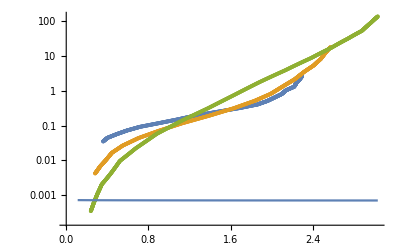

```mathematica
Show[refReverseIsothermLogPlot,Plot[testFit/.{th->m},{m,1.11436*^-8,3.03*^-7}]]
```

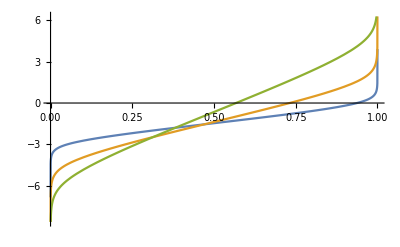

```mathematica
Plot[{modifiedFrumkinFit1mA,modifiedFrumkinFit2mA,modifiedFrumkinFit4mA},{th,0,1}]
```

```mathematica
Length[refReverseLogIsotherm4mANormCorrected]
```

823

```mathematica
modifiedFrumkinFit4mA=Fit[refReverseLogIsotherm4mANormCorrected[[2;;(Length[refReverseLogIsotherm4mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFit2mA=Fit[refReverseLogIsotherm2mANormCorrected[[2;;(Length[refReverseLogIsotherm2mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-3.42162+4.10408 th+0.419436 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFit1mA=Fit[refReverseLogIsotherm1mANormCorrected[[2;;(Length[refReverseLogIsotherm1mANormCorrected]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-2.34523+1.77185 th+0.252778 (-Log[1-th]+Log[th])

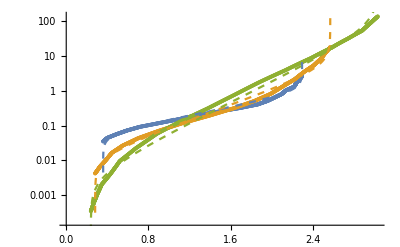

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mA/.th->((m-First[refReverseLogIsotherm1mA][[1]])/(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])),
modifiedFrumkinFit2mA/.th->((m-First[refReverseLogIsotherm2mA][[1]])/(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])),
modifiedFrumkinFit4mA/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

```mathematica
modifiedFrumkinFit4mAAbsolute=Fit[refReverseLogIsotherm4mANormCorrectedAbsolute[[2;;(Length[refReverseLogIsotherm4mANormCorrectedAbsolute]-1)]],{1,
th,
Log[th]-Log[1-th]},th]
```

-4.3502+7.40358 th+0.555019 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFit2mAAbsolute=Fit[refReverseLogIsotherm2mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

-3.7303+6.09643 th+0.42402 (-Log[1-th]+Log[th])

```mathematica
modifiedFrumkinFit1mAAbsolute=Fit[refReverseLogIsotherm1mANormCorrectedAbsolute,{1,
th,
Log[th]-Log[1-th]},th]
```

-3.68507+5.55239 th-0.0939813 (-Log[1-th]+Log[th])

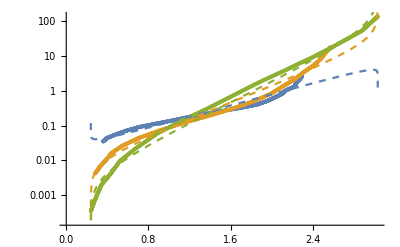

```mathematica
Show[refReverseIsothermLogPlot,Plot[{modifiedFrumkinFit1mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit2mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),
modifiedFrumkinFit4mAAbsolute/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]]))},
{m,0,Last[refReverseLogIsotherm4mA][[1]]},PlotStyle->Dashed]]
```

```mathematica
modifiedBockrisSwinkelFit=Fit[refReverseLogIsotherm4mANormCorrected[[2;;822]],{1,
th,
(Log[th]-n*Log[1-th]+(n-1)*Log[th+n*(1-th)]-n*Log[n])/.n->10},th]
```

-6.39269+11.4191 th-0.00556767 (-10 Log[10]-10 Log[1-th]+Log[th]+9 Log[10 (1-th)+th])

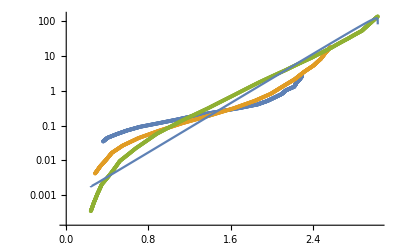

```mathematica
Show[refReverseIsothermLogPlot,Plot[modifiedBockrisSwinkelFit/.th->((m-First[refReverseLogIsotherm4mA][[1]])/(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])),{m,0,m0max}]]
```

```mathematica
modifiedFrunkinIsotherm1mA[c_]:=FindRoot[modifiedFrumkinFit1mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm2mA[c_]:=FindRoot[modifiedFrumkinFit2mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm4mA[c_]:=FindRoot[modifiedFrumkinFit4mA==Log[c],{th,0.5}]
```

```mathematica
modifiedFrunkinIsotherm1mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit1mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm2mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit2mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm4mANSolve[c_]:=Quiet[NSolve[modifiedFrumkinFit4mA==Log[c],th,Reals]][[1]]
```

```mathematica
modifiedFrunkinIsotherm4mA[0.4]
```

{th→0.472171}

```mathematica
modifiedFrunkinIsotherm1mA[0.3]
```

{th→0.591371}

```mathematica
modifiedFrunkinIsotherm4mANSolve[0.001]
```

{th→0.00995386}

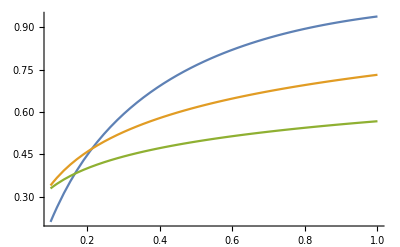

```mathematica
Plot[{th/.modifiedFrunkinIsotherm1mA[c],th/.modifiedFrunkinIsotherm2mA[c],th/.modifiedFrunkinIsotherm4mA[c]},{c,0.1,1}]
```

```mathematica
Plot[{modifiedFrunkinIsotherm1mA[c]},{c,0.1,1}]
```

-Graphics-

```mathematica
modifiedFrunkinIsotherm1mA[0.06]
```

{th→0.0814368}

```mathematica
fit1mA = Table[{dat1mA[[n,1]],N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]},{n,1,Length[dat1mA]}];
```

```mathematica
fit2mA = Table[{dat2mA[[n,1]],N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]},{n,1,Length[dat2mA]}];
```

```mathematica
fit4mA = Table[{dat4mA[[n,1]],N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]},{n,1,Length[dat4mA]}];
```

```mathematica
massPrediction1mA = Table[{dat1mA[[n,1]],
N[th/.modifiedFrunkinIsotherm1mANSolve[dat1mA[[n,2]]]]
*(Last[refReverseLogIsotherm1mA][[1]]-First[refReverseLogIsotherm1mA][[1]])+First[refReverseLogIsotherm1mA][[1]]},{n,1,Length[dat1mA]}];
```

```mathematica
massPrediction2mA = Table[{dat2mA[[n,1]],
N[th/.modifiedFrunkinIsotherm2mANSolve[dat2mA[[n,2]]]]
*(Last[refReverseLogIsotherm2mA][[1]]-First[refReverseLogIsotherm2mA][[1]])+First[refReverseLogIsotherm2mA][[1]]},{n,1,Length[dat2mA]}];
```

```mathematica
massPrediction4mA = Table[{dat4mA[[n,1]],
N[th/.modifiedFrunkinIsotherm4mANSolve[dat4mA[[n,2]]]]
*(Last[refReverseLogIsotherm4mA][[1]]-First[refReverseLogIsotherm4mA][[1]])+First[refReverseLogIsotherm4mA][[1]]},{n,1,Length[dat4mA]}];
```

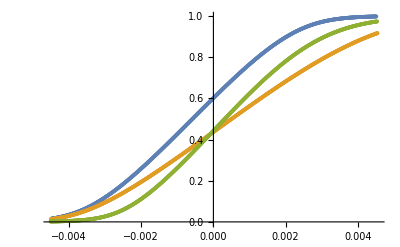

```mathematica
ListPlot[{fit1mA,fit2mA,fit4mA}]
```

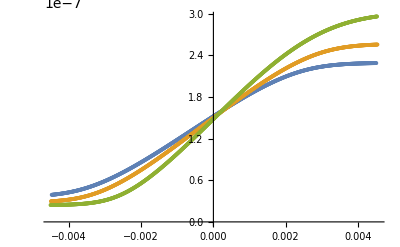

```mathematica
massPredictionPlot=ListPlot[{massPrediction1mA,massPrediction2mA,massPrediction4mA},PlotStyle->Line]
```

```mathematica
Show
```

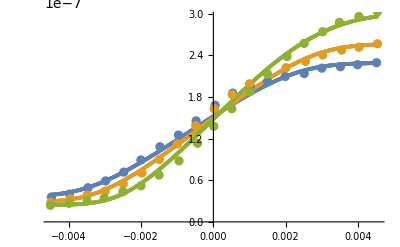

```mathematica
Show[massPredictionPlot,trueMassPlot]
```